# Data Set 1

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;
```

## Data Import

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
10/19/2015 09:56:53
$MEAS_TIM:
3600 3733
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

\begin{array}{c}
 \text{$\$$SPEC$\_$ID:} \\
 \text{Molnar Range} \\
 \text{$\$$SPEC$\_$REM:} \\
 \text{DET$\#$ 1} \\
 \text{DETDESC$\#$ HPGe Detector 1} \\
 \text{AP$\#$ GammaVision Version 6.07} \\
 \text{$\$$DATE$\_$MEA:} \\
 \text{10/19/2015 09:56:53} \\
 \text{$\$$MEAS$\_$TIM:} \\
 \text{3600 3733} \\
 \text{$\$$DATA:} \\
 \text{0 8191} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{$\$$ROI:} \\
 0 \\
 \text{$\$$PRESETS:} \\
 \text{Live Time} \\
 3600 \\
 0 \\
 \text{$\$$ENER$\_$FIT:} \\
 \text{0.137869 0.366631} \\
 \text{$\$$MCA$\_$CAL:} \\
 3 \\
 \text{1.378689E-001 3.666307E-001 -4.415950E-008 keV} \\
 \text{$\$$SHAPE$\_$CAL:} \\
 3 \\
 \text{2.301834E+000 9.195991E-004 -5.357180E-008} \\
\end{array}

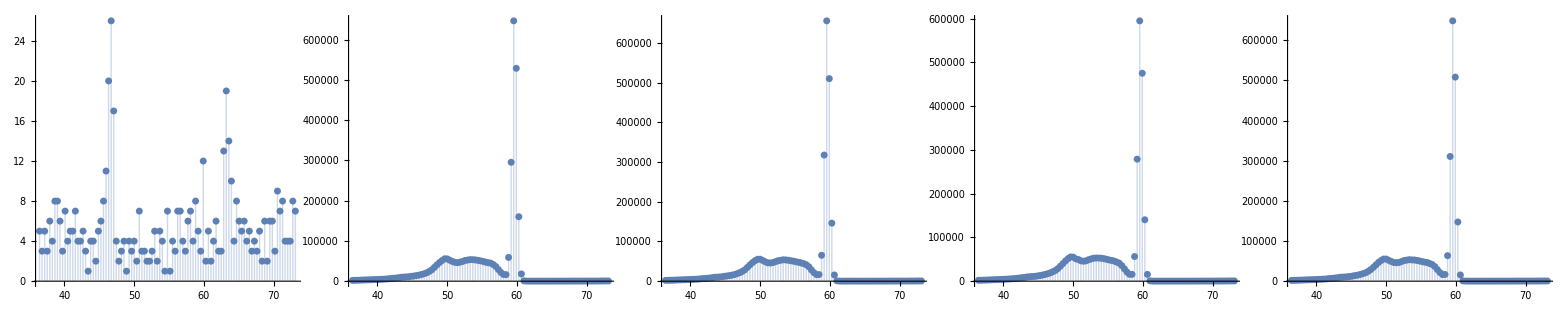

```mathematica
set=1;
filenames[set]={
"Background-10192015.Spe",
"Am-241-1hr-10192015.Spe",
"Am-241-1hrTrial2-10192015.Spe",
"Am-241-ThickFilm-1hr-10192015.Spe",
"Am-241-ThinFilm-1hr-10192015.Spe"};

m=Length[filenames[set]]-1;
For[n=1,n≤m+1,n++,
imported=Import[filenames[set][[n]],"Data"];
times=ToExpression[StringSplit[imported[[10]]]];
If[n==2,
Print[TableForm[imported[[;;15]]]];
Print[TableForm[imported[[-16;;]]]];
Print[TeXForm[TableForm[Drop[imported,{16,Length[imported]-16}]]]];
];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
energy[set,n-1]=ToExpression[StringSplit[imported[[-7]]]];
data[set,n-1]=Table[{i,energy[set,n-1][[1]]+energy[set,n-1][[2]](i-1),freq[[i]]},{i,Length[freq]}];
]
Grid[{Table[ListPlot[data[set,i][[100;;200,{2,3}]],ImageSize->Medium,PlotRange->All,Filling->Bottom],{i,0,m}]}]
Clear[n,imported,times,deadtime,freq]
```

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Cubic Fit

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

| Estimate | Standard Error | t-Statistic | P-Value
a | 467.296 | 292.164 | 1.59943 | 0.153759
b | -79938.5 | 51243.7 | -1.55997 | 0.162733
c | 4.54253×10^6 | 2.99455×10^6 | 1.51693 | 0.17307
d | -8.57094×10^7 | 5.83051×10^7 | -1.47002 | 0.185019
mu | 59.6425 | 0.00089794 | 66421.5 | 4.63038×10^-32
sigma | 0.368453 | 0.00140164 | 262.874 | 3.04375×10^-15
p | 673782. | 2212.75 | 304.5 | 1.08783×10^-15

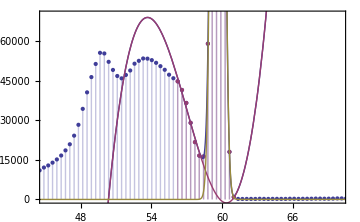

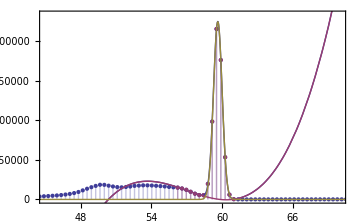

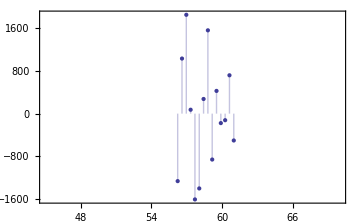

```mathematica
region={154,167};
Clear[a,b,c,d,mu,sigma,p]
viewingregion={50,200};viewingrange={45,70};imagesize=Medium;fontsize=12;theme="Classic";

guess={{a,361},{b,-61524},{c,3473469},{d,-65035121},{mu,59.6},{sigma,0.37},{p,670000}};

k=1;
cubic[set,k]=NonlinearModelFit[data[set,k][[region[[1]];;region[[2]],{2,3}]],a x^3+b x^2+c x+d+F[x,mu,sigma,p],guess,x];

cubic[set,k]["ParameterTable"]
cubicparams[set,k]=cubic[set,k]["BestFitParameters"][[All,2]];

Show[ListPlot[{data[set,k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[set,k][[region[[1]];;region[[2]],{2,3}]]},Filling->Axis,PlotRange->All,PlotTheme->theme],Plot[{cubic[set,k]["BestFit"],cubicparams[set,k][[1]]x^3+cubicparams[set,k][[2]]x^2+cubicparams[set,k][[3]]x+cubicparams[set,k][[4]],F[x,cubicparams[set,k][[-3]],cubicparams[set,k][[-2]],cubicparams[set,k][[-1]]]},{x,-10,100},PlotTheme->theme],PlotRange->{viewingrange,{0,70000}},Frame->{{True,False},{True,False}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

Show[ListPlot[{data[set,k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[set,k][[region[[1]];;region[[2]],{2,3}]]},Filling->Axis,PlotRange->All,PlotTheme->theme],Plot[{cubic[set,k]["BestFit"],cubicparams[set,k][[1]]x^3+cubicparams[set,k][[2]]x^2+cubicparams[set,k][[3]]x+cubicparams[set,k][[4]],F[x,cubicparams[set,k][[-3]],cubicparams[set,k][[-2]],cubicparams[set,k][[-1]]]},{x,-10,100},PlotTheme->theme],PlotRange->{viewingrange,{0,700000}},Frame->{{True,False},{True,False}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

ListPlot[Join[Table[{energy[set,k][[1]]+energy[set,k][[2]](i-1)},{i,region[[1]],region[[2]]}],Transpose[{cubic[set,k]["FitResiduals"]}],2],Filling->Axis,Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->True,PlotRange->{viewingrange,All},PlotTheme->theme,ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]
```

## Gaussian Fits

```mathematica
mu={24.2,48.4,49.7,53.2,56.0,59.6};
sigma={0.4,5.4,1.4,1.3,1.5,0.4};
a={6000,15000,30000,30000,30000,730000};
n=Length[mu];region={1,200};
symbol={"μ","σ","a","I"};
thickness={40,0.01};area={10.0,0.1};mass={2.0,0.1};
runs[set]={"Source 1","Source 2","Thick","Thin"};

For[k=1,k≤m,k++,
model[set,k]=NonlinearModelFit[data[set,k][[region[[1]];;region[[2]],{2,3}]],G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];

params[set,k]=model[set,k]["BestFitParameters"][[All,2]];
paramerrors[set,k]=model[set,k]["ParameterErrors"];

modeldata=Table[err[F,{i,0},{params[set,k][[n]],paramerrors[set,k][[n]]},{params[set,k][[2n]],paramerrors[set,k][[2n]]},{params[set,k][[3n]],paramerrors[set,k][[3n]]}],{i,Table[data[set,k][[i[[1]],2]],{i,Position[data[set,k][[;;200,2]],_?(params[set,k][[n]]-2*fwhm[params[set,k][[2n]]]<#<params[set,k][[n]]+2*fwhm[params[set,k][[2n]]]&)]}]}];
intensity[set,k]={Total[modeldata[[All,1]]*energy[set,k][[2]]],Sqrt[Total[(modeldata[[All,2]]*energy[set,k][[2]])^2]]};
Print[TableForm[Insert[Insert[

Table[{symbol[[i/n]],params[set,k][[i]],paramerrors[set,k][[i]],100*paramerrors[set,k][[i]]/params[set,k][[i]]},{i,{n,2n,3n}}],

Join[{symbol[[4]]},intensity[set,k],{100*intensity[set,k][[2]]/intensity[set,k][[1]]}],4]
,{{},{"Value"},{"Error"},{"Percent Error"}},1]]];
];Clear[modeldata]

Print[TableForm[Insert[Table[Join[{runs[set][[i]]},intensity[set,i],{100*intensity[set,i][[2]]/intensity[set,i][[1]]}],{i,1,m}],{{},{"Intensity"},{"Error"},"Percent Error"},1]]]

Print["\nTrial 1"]
atten[set,1]=err[coeff,intensity[set,1],intensity[set,3],thickness];
Print["attenuation coefficient = ",Join[atten[set,1],{100*atten[set,1][[2]]/atten[set,1][[1]]}]]
thin[set,1]=err[coeff,intensity[set,1],intensity[set,4],atten[set,1]];Print["thin foil measurement = ",Join[thin[set,1],{100*thin[set,1][[2]]/thin[set,1][[1]]}]]

Print["\nTrial 2"]
atten[set,2]=err[coeff,intensity[set,2],intensity[set,3],thickness];
Print["attenuation coefficient = ",Join[atten[set,2],{100*atten[set,2][[2]]/atten[set,2][[1]]}]]
thin[set,2]=err[coeff,intensity[set,2],intensity[set,4],atten[set,2][set,2]];Print["thin foil measurement = ",Join[thin[set,2],{100*thin[set,2][[2]]/thin[set,2][[1]]}]]
```

| Value | Error | Percent Error
μ | 59.6414 | 0.000539345 | 0.000904313
σ | 0.367201 | 0.000601985 | 0.163939
a | 671576. | 876.344 | 0.130491
I | 618143. | 718.15 | 0.116179

| Value | Error | Percent Error
μ | 59.6216 | 0.000540992 | 0.000907375
σ | 0.36809 | 0.000602032 | 0.163556
a | 671878. | 877.387 | 0.130587
I | 619914. | 719.346 | 0.11604

| Value | Error | Percent Error
μ | 59.6325 | 0.000559756 | 0.000938677
σ | 0.367305 | 0.000622374 | 0.169444
a | 613824. | 830.203 | 0.135251
I | 565142. | 679.972 | 0.120319

| Value | Error | Percent Error
μ | 59.6251 | 0.000533375 | 0.000894548
σ | 0.367846 | 0.000594345 | 0.161574
a | 665615. | 857.997 | 0.128903
I | 613729. | 703.294 | 0.114594

| Intensity | Error | Percent Error
Source 1 | 618143. | 718.15 | 0.116179
Source 2 | 619914. | 719.346 | 0.11604
Thick | 565142. | 679.972 | 0.120319
Thin | 613729. | 703.294 | 0.114594

Trial 1

attenuation coefficient = {0.00224109,0.0000418174,1.86594}

thin foil measurement = {3.19806,0.730589,22.8447}

Trial 2

attenuation coefficient = {0.00231263,0.0000417935,1.80719}

thin foil measurement = {0.0100286,0.0201234,200.66}

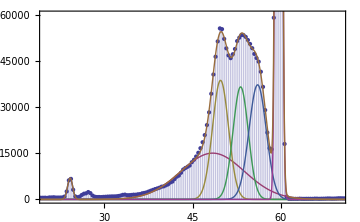
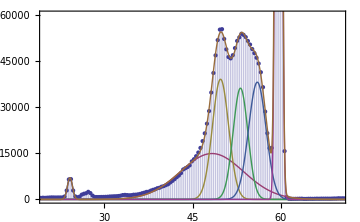
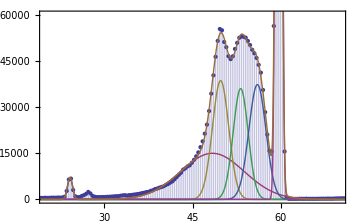
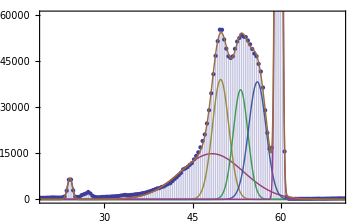
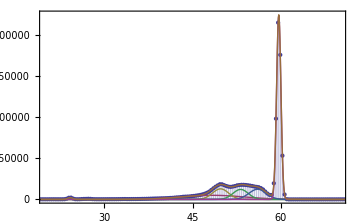
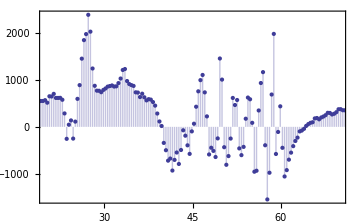
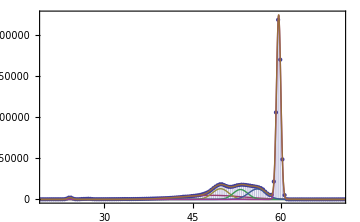
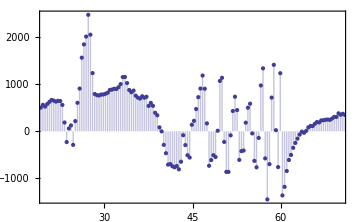
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics-

```mathematica
viewingrange={20,70};
theme="Classic";imagesize=Medium;fontsize=12;

Grid[Transpose[Table[{Show[ListPlot[data[set,k][[region[[1]];;region[[2]],{2,3}]],Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[set,k][[i]],params[set,k][[i+n]],params[set,k][[i+2n]]],{i,1,n}],{G[x,params[set,k][[;;n]],params[set,k][[n+1;;2n]],params[set,k][[2n+1;;3n]]]}],{x,-10,200},PlotRange->All,PlotTheme->theme],Frame->{{True,False},{True,False}},PlotRange->{viewingrange,{0,60000}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}],

Show[ListPlot[data[set,k][[region[[1]];;region[[2]],{2,3}]],Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[set,k][[i]],params[set,k][[i+n]],params[set,k][[i+2n]]],{i,1,n}],{G[x,params[set,k][[;;n]],params[set,k][[n+1;;2n]],params[set,k][[2n+1;;3n]]]}],{x,-10,200},PlotRange->All,PlotTheme->theme],Frame->{{True,False},{True,False}},PlotRange->{viewingrange,All},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

ListPlot[Join[Table[{energy[set,k][[1]]+energy[set,k][[2]](i-1)},{i,region[[1]],region[[2]]}],Transpose[{model[set,k]["FitResiduals"]}],2],Filling->Axis,Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->True,PlotRange->{viewingrange,All},PlotTheme->theme,ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]},{k,1,4}]]]
```